```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[Λ, _]]
Symbolize[Subscript[I, _]]
Symbolize[Subscript[V, _]]
Symbolize[Subscript[J, _]]
Symbolize[Subscript[v, _]]
Symbolize[Subscript[i, _]]
Symbolize[Subscript[j, _]]
Symbolize[Subscript[μ, e]]
Notation[OverDot[x_] ⟺ Dt[x_, t]]
Symbolize[Subscript[U, T]]
```

```mathematica
κ/:Dt[κ, t]=0;
$Assumptions=κ>0&& c>0&&Subscript[U, T]>0 && Subscript[I, leak]>0 && Subscript[I, in]>0 && Subscript[I, mem]>0 && Subscript[Λ, in]>0&& Subscript[Λ, fb]>0;
$Assumptions = $Assumptions && Subscript[J, mem]>0;
```

# Statistical Model of the FDSOI Neuron

## LPF

The LPF’s equation is:

Steps :

```mathematica
iLPFDyn[ Subscript[I, mem]:_, Subscript[Λ, in]:_, Subscript[I, in]:_, Subscript[I, leak]:_, κ_]:=(c Subscript[U, T])/(κ Subscript[I, leak]) OverDot[Subscript[I, mem]]==-Subscript[I, mem]+Subscript[Λ, in] Subscript[I, in](Subscript[I, leak]/Subscript[I, mem])^(1/κ-1)
τ[Subscript[I, leak]:_]:= (c Subscript[U, T])/(κ Subscript[I, leak])
iLeak[τ_]:= (c Subscript[U, T])/(κ τ)
```

```mathematica
iLPFDyn[Subscript[I, mem], Subscript[Λ, in], Subscript[I, in], Subscript[I, leak], κ]
```

(c U_T OverDot[I_mem])/(I_leak κ)==-I_mem+I_in (I_leak/I_mem)^(-1+1/κ) Λ_in

where

```mathematica
τ==τ[ Subscript[I, leak]]
```

τ==(c U_T)/(I_leak κ)

Under steady-state, we have I_mem as

Steps :

```mathematica
tDyn = iLPFDyn[Subscript[I, mem], Subscript[Λ, in], Subscript[I, in], Subscript[I, leak], κ] ;
tLHS = First[tDyn];
tRHS = Last[tDyn];
imSS[Subscript[I, leak]:_, Subscript[I, in]:_, Subscript[Λ, in]:_]:=Evaluate[Last[Last[Reduce[tRHS==0 &&$Assumptions, Subscript[I, mem],Reals]]]]
```

```mathematica
Subscript[I, memSS]==imSS[Subscript[I, leak], Subscript[I, in], Subscript[Λ, in]]
```

I_memSS==I_leak (I_leak/(I_in Λ_in))^-κ

Substituting I_mem→ J_mem^κ, we get

Steps :

```mathematica
FullSimplify[(Subscript[I, mem]^(1/κ-1)#)&/@{tLHS, tRHS }];
tMod = FullSimplify[%/.Subscript[I, mem]-> Subscript[J, mem]^κ];
jLPFDyn[ Subscript[J, mem]:_, Subscript[Λ, in]:_, Subscript[I, in]:_, Subscript[I, leak]:_, κ_]:=Evaluate[tMod[[1]]==tMod[[2]]]
jMem[Subscript[I, mem]:_]:= Subscript[I, mem]^(1/κ);
iMem[Subscript[J, mem]:_]:= Overscript[Subscript[J, mem], κ];
```

```mathematica
jLPFDyn[Subscript[J, mem], Subscript[Λ, in], Subscript[I, in], Subscript[I, leak], κ]
```

(c U_T OverDot[J_mem])/I_leak==-J_mem+I_in I_leak^(-1+1/κ) Λ_in

Divide by I_leak^(1/κ) to obtain the dimensionless form:

Steps :

```mathematica
tFull=jLPFDyn[Subscript[J, mem], Subscript[Λ, in], Subscript[I, in], Subscript[I, leak], κ];
tLHS=First[tFull]/.Subscript[I, leak]-> iLeak[τ/κ];  (* original τ is rescaled by κ *)
tRHS=Last[tFull];
tSol=FullSimplify[{tLHS, tRHS}/Subscript[I, leak]^(1/κ)];
vMem[Subscript[J, mem]:_, Subscript[I, leak]:_]:=Subscript[J, mem]/Subscript[I, leak]^(1/κ); jMem[Subscript[v, mem]:_, Subscript[I, leak]:_]:=Subscript[v, mem] Subscript[I, leak]^(1/κ);
iIn[Subscript[I, in]:_, Subscript[I, leak]:_, Subscript[Λ, in]:_]:=(Subscript[I, in] Subscript[Λ, in])/Subscript[I, leak];iBiasIn[Subscript[i, in]:_, Subscript[I, leak]:_, Subscript[Λ, in]:_]:=1/Subscript[Λ, in] Subscript[i, in] Subscript[I, leak];
(* tSol=Refine[tSol/.{Subscript[J, mem]-> Subscript[v, mem] Subscript[I, leak]^(1/κ), Subscript[I, in]-> 1/Subscript[Λ, in] Subscript[i, in] Subscript[I, leak]}, OverDot[Subscript[I, leak]]==0]; *)
tSol=Refine[tSol/.{Subscript[J, mem]-> Subscript[v, mem] Subscript[I, leak]^(1/κ)}, OverDot[Subscript[I, leak]]==0];
```

```mathematica
tSol[[1]]==tSol[[2]]
```

τ OverDot[v_mem]==-v_mem+(I_in Λ_in)/I_leak

where

```mathematica
τ==τ[ Subscript[I, leak]/κ]
```

τ==(c U_T)/I_leak

## Soma

Soma circuit’s dynamics is given by

Steps :

```mathematica
iSomaDyn[ Subscript[I, mem]:_, Subscript[Λ, in]:_, Subscript[Λ, fb]:_, Subscript[I, in]:_, Subscript[I, leak]:_, κ_]:=(c Subscript[U, T])/(κ Subscript[I, leak]) OverDot[Subscript[I, mem]]==-Subscript[I, mem] + Subscript[Λ, in] Subscript[I, in](Subscript[I, leak]/Subscript[I, mem])^(1/κ-1)+ Subscript[Λ, fb] Subscript[I, mem]^2/Subscript[I, leak]
```

```mathematica
iSomaDyn[Subscript[I, mem], Subscript[Λ, in],Subscript[Λ, fb], Subscript[I, in], Subscript[I, leak], κ]
```

(c U_T OverDot[I_mem])/(I_leak κ)==-I_mem+(I_mem^2 Λ_fb)/I_leak+I_in (I_leak/I_mem)^(-1+1/κ) Λ_in

Substituting I_mem→ J_mem^κ, we get

Steps :

```mathematica
tFull = iSomaDyn[Subscript[I, mem], Subscript[Λ, in], Subscript[Λ, fb], Subscript[I, in], Subscript[I, leak], κ] ;
tLHS = First[tFull];
tRHS = Last[tFull];
FullSimplify[(Subscript[I, mem]^(1/κ-1)#)&/@{tLHS, tRHS }];
tMod = FullSimplify[%/.Subscript[I, mem]-> Subscript[J, mem]^κ];
jSomaDyn[ Subscript[J, mem]:_, Subscript[Λ, in]:_,Subscript[Λ, fb]:_, Subscript[I, in]:_, Subscript[I, leak]:_, κ_]:=Evaluate[tMod[[1]]==ExpandAll[tMod[[2]]]]
```

```mathematica
jSomaDyn[Subscript[J, mem], Subscript[Λ, in], Subscript[Λ, fb],Subscript[I, in], Subscript[I, leak], κ]
```

(c U_T OverDot[J_mem])/I_leak==-J_mem+(J_mem^(1+κ) Λ_fb)/I_leak+I_in I_leak^(-1+1/κ) Λ_in

In the J-space, the membrane threshold is at

Steps :

```mathematica
tFull = jSomaDyn[Subscript[J, mem], Subscript[Λ, in], Subscript[Λ, fb], Subscript[I, in], Subscript[I, leak], κ] ;
tLHS = First[tFull];
tRHS = Last[tFull];
tDer =D[tRHS, Subscript[J, mem]];
jMemTh[Subscript[I, leak]:_, Subscript[Λ, fb]:_, κ_]:=Evaluate[FullSimplify[Subscript[J, mem]/.Solve[tDer==0, Subscript[J, mem]][[1]]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Subscript[J, mth]==jMemTh[Subscript[I, leak], Subscript[Λ, fb], κ]
```

J_mth==(((1+κ) Λ_fb)/I_leak)^(-1/κ)

Then, the minimum input current needed to cause bifurcation is

Steps :

```mathematica
tFull = jSomaDyn[Subscript[J, mem], Subscript[Λ, in], Subscript[Λ, fb], Subscript[I, in], Subscript[I, leak], κ] ;
tLHS = First[tFull];
tRHS = Last[tFull];
iBiasTh[Subscript[I, leak]:_,Subscript[Λ, in]:_,Subscript[Λ, fb]:_]:=Evaluate[Subscript[I, in]/.FullSimplify[Solve[Evaluate[tRHS/.Subscript[J, mem]-> jMemTh[Subscript[I, leak], Subscript[Λ, fb], κ]]==0, Subscript[I, in]]][[1]]]
```

```mathematica
Subscript[I, inth]==iBiasTh[Subscript[I, leak],Subscript[Λ, in],Subscript[Λ, fb]]
```

I_inth==(I_leak κ Λ_fb ((1+κ) Λ_fb)^(-(1+κ)/κ))/Λ_in

Normalizing the J-space soma dynamics with J_mth gives:

Steps :

```mathematica
tFull=jSomaDyn[Subscript[J, mem],Subscript[Λ, in],Subscript[Λ, fb],Subscript[I, in],Subscript[I, leak],κ];
tLHS=First[tFull];
tRHS=Last[tFull];
tSol=FullSimplify[Refine[tFull/.{Subscript[J, mem]->Subscript[v, mem] jMemTh[Subscript[I, leak],Subscript[Λ, fb],κ]},OverDot[Subscript[I, leak]]==0&&OverDot[Subscript[Λ, fb]]==0]];
vMem[Subscript[J, mem]:_,Subscript[I, leak]:_,Subscript[Λ, fb]:_]:=FullSimplify[Subscript[J, mem]/jMemTh[Subscript[I, leak],Subscript[Λ, fb],κ]];
jMem[Subscript[v, mem]:_,Subscript[I, leak]:_,Subscript[Λ, fb]:_]:=FullSimplify[Subscript[v, mem] jMemTh[Subscript[I, leak],Subscript[Λ, fb],κ]];
iIn[Subscript[I, in]:_,Subscript[I, leak]:_,Subscript[Λ, in]:_,Subscript[Λ, fb]:_]:=FullSimplify[(Subscript[I, in] Subscript[I, leak]^(-1+1/κ) Subscript[Λ, in])/jMemTh[Subscript[I, leak],Subscript[Λ, fb],κ]];
iBiasIn[Subscript[i, in]:_,Subscript[I, leak]:_,Subscript[Λ, in]:_,Subscript[Λ, fb]:_]:=FullSimplify[(Subscript[i, in] jMemTh[Subscript[I, leak],Subscript[Λ, fb],κ])/(Subscript[I, leak]^(-1+1/κ) Subscript[Λ, in])];
tSol=(Collect[FullSimplify[# 1/(1+κ)1/Subscript[I, leak]], {Subscript[I, in], Subscript[v, mem]}, Simplify]&)/@{First[tSol], Last[tSol]};
iSomaNormDyn[Subscript[v, mem]:_, Subscript[I, leak]:_, Subscript[I, in]:_, Subscript[Λ, in]:_]:=Evaluate[tSol[[2]]==Expand[tSol[[1]]]]
iInNormalization[Subscript[I, leak]:_, Subscript[Λ, in]:_]:=Evaluate[Coefficient[tSol[[1]], Subscript[I, in]]];
```

```mathematica
iSomaNormDyn[Subscript[v, mem], Subscript[I, leak], Subscript[I, in]+Subscript[I, bg], Subscript[Λ, in]]
```

(c U_T OverDot[v_mem])/I_leak==-v_mem+v_mem^(1+κ)/(1+κ)+((I_bg+I_in) ((1+κ) Λ_fb)^(1/κ) Λ_in)/I_leak

In dimensionless units, the input current needed to cause bifurcation is

```mathematica
FullSimplify[iIn [iBiasTh[Subscript[I, leak],Subscript[Λ, in],Subscript[Λ, fb]], Subscript[I, leak],Subscript[Λ, in],Subscript[Λ, fb]]]
```

κ/(1+κ)

## Synapse connected to Soma

Steps :

```mathematica
tFull=iLPFDyn[Subscript[I, syn], Subscript[Λ, synin], Subscript[I, synin], Subscript[I, leaksyn], κ];
tNorm=iInNormalization[Subscript[I, leaksoma], Subscript[Λ, somain]] ;
tCancel1=Subscript[Λ, somain]/(Subscript[I, leaksoma](Subscript[Λ, fb]+κ Subscript[Λ, fb])^(-1/κ));
vSyn[Subscript[I, syn]:_, Subscript[I, leaksoma]:_, Subscript[Λ, somain]:_]:=Evaluate[Subscript[I, syn] tNorm];
iSyn[Subscript[v, syn]:_, Subscript[I, leaksoma]:_, Subscript[Λ, somain]:_]:=Evaluate[Subscript[v, syn]/tNorm];
t1=(ExpandAll[FullSimplify[Refine[(# tCancel1)/.Subscript[I, syn]-> Subscript[v, syn]/tNorm, OverDot[Subscript[I, leaksoma]]==0&&OverDot[Subscript[Λ, fb]]==0&&OverDot[Subscript[Λ, somain]]==0]]])&/@{First[tFull], Last[tFull]};
tCancel2=Subscript[v, syn]^(1/κ-1);
t2=ExpandAll[FullSimplify[# tCancel2, Subscript[v, syn]>0&& κ>0]]&/@t1;
tSol=FullSimplify[#/.Subscript[v, syn]-> Subscript[j, syn]^κ, Subscript[j, syn]>0&&κ>0]&/@t2;
iSynNormIn[Subscript[I, synin]:_, Subscript[I, leaksyn]:_, Subscript[I, leaksoma]:_, Subscript[Λ, somain]:_,Subscript[Λ, synin]:_]:= Evaluate[Coefficient[tSol[[2]], Subscript[I, synin]] Subscript[I, synin]]
iSynIn[Subscript[i, synin]:_, Subscript[I, leaksyn]:_, Subscript[I, leaksoma]:_, Subscript[Λ, somain]:_,Subscript[Λ, synin]:_]:=Evaluate[Subscript[i, synin]/Coefficient[tSol[[2]], Subscript[I, synin]]]
iSynNormDyn[Subscript[j, syn]:_,Subscript[I, synin]:_, Subscript[I, leaksyn]:_,  Subscript[I, leaksoma]:_]:=Evaluate[tSol[[1]]==tSol[[2]]];
```

Since synaptic input to Soma is a current injection, normalize the Synapse’s dynamic equation

```mathematica
tFull
```

(c U_T OverDot[I_syn])/(I_leaksyn κ)==-I_syn+(I_leaksyn/I_syn)^(-1+1/κ) I_synin Λ_synin

by dividing with

```mathematica
tNorm
```

(((1+κ) Λ_fb)^(1/κ) Λ_somain)/I_leaksoma

This gives the dimensionless form

```mathematica
t1[[1]]==t1[[2]]
```

(c U_T OverDot[v_syn])/(I_leaksyn κ)==-v_syn+(I_synin v_syn (Λ_fb+κ Λ_fb)^(1/κ^2) ((I_leaksyn Λ_somain)/(I_leaksoma v_syn))^(1/κ) Λ_synin)/I_leaksyn

Using the substitution v_syn→ j_syn^κ, this simplifies to

```mathematica
iSynNormDyn[Subscript[j, syn],Subscript[I, synin], Subscript[I, leaksyn],  Subscript[I, leaksoma]]
```

(c U_T OverDot[j_syn])/I_leaksyn==-j_syn+(I_synin ((1+κ) Λ_fb)^(1/κ^2) ((I_leaksyn Λ_somain)/I_leaksoma)^(1/κ) Λ_synin)/I_leaksyn

## Full Model

```mathematica
tFullSoma=iSomaNormDyn[Subscript[v, mem], Subscript[I, leaksoma], iSyn[Subscript[v, syn], Subscript[I, leaksoma], Subscript[Λ, somain]]+Subscript[I, bg], Subscript[Λ, somain]];
tSol=Expand[FullSimplify[ExpandAll[#]]]&/@{First[tFullSoma], Last[tFullSoma]};
tSol[[1]]==tSol[[2]]
```

(c U_T OverDot[v_mem])/I_leaksoma==-v_mem+v_syn+v_mem^(1+κ)/(1+κ)+(I_bg ((1+κ) Λ_fb)^(1/κ) Λ_somain)/I_leaksoma

```mathematica
Subscript[v, syn]-> Subscript[j, syn]^κ
```

v_syn→j_syn^κ

```mathematica
iSynNormDyn[Subscript[j, syn],Subscript[I, synin], Subscript[I, leaksyn],  Subscript[I, leaksoma]]
```

(c U_T OverDot[j_syn])/I_leaksyn==-j_syn+(I_synin ((1+κ) Λ_fb)^(1/κ^2) ((I_leaksyn Λ_somain)/I_leaksoma)^(1/κ) Λ_synin)/I_leaksyn

## Steady-State Behavior

For the dimensionless Synapse model, j_syn=i_synin under steady-state. Then,

```mathematica
Subscript[v, syn]==vSyn[Subscript[I, syn],Subscript[I, leaksoma],Subscript[Λ, somain]]
```

v_syn==(I_syn ((1+κ) Λ_fb)^(1/κ) Λ_somain)/I_leaksoma

```mathematica
tFull=vSyn[Subscript[I, syn],Subscript[I, leaksoma],Subscript[Λ, somain]]==FullSimplify[iSynNormIn[Subscript[I, synin], Subscript[I, leaksyn], Subscript[I, leaksoma], Subscript[Λ, somain],Subscript[Λ, synin]]^κ, Subscript[I, leaksyn]>0&&Subscript[Λ, somain]>0&&Subscript[I, leaksoma]>0&&κ>0];
tCancel=Subscript[I, leaksoma]/(((1+κ) Subscript[Λ, fb])^(1/κ)Subscript[Λ, somain]);
tSol=FullSimplify[# tCancel]&/@{First[tFull], Last[tFull]};
tSol[[1]]==tSol[[2]]
```

I_syn==I_leaksyn ((I_synin Λ_synin)/I_leaksyn)^κ

## Mismatch

## Introduction

Assuming the mismatch is in threshold and has a Normal distribution, the mismatch in the current has a Lognormal distribution.

Steps :

```mathematica
μe[temp_]:= μ0 temp^-2.4
ut[temp_]:=Evaluate[(k temp)/q/.{k-> First[UnitConvert[Quantity[1, "BoltzmannCostant"]]], q-> First[UnitConvert[Quantity[1, "ElectronicCharge"]]]}]
id[Subscript[V, gs]:_]:= w/l Subscript[μ, e] Cox Subscript[U, T]^2(1/κ-1)ⅇ^((-κ Subscript[V, t])/Subscript[U, T]) ⅇ^((κ Subscript[V, gs]-(1-κ) (Subscript[V, s]-Subscript[V, b]))/Subscript[U, T])

vDist[Subscript[I, in]:_, μ_, σ_] :=NormalDistribution[Log[Subscript[I, in]]+μ, σ]
iDist[Subscript[I, in]:_, μ_, σ_] := LogNormalDistribution[Log[Subscript[I, in]]+μ, σ]
```

```mathematica
Log[Subscript[I, d]]==PowerExpand[Log[Simplify[id[Subscript[V, gs]],TransformationFunctions->{Automatic,#/. w/l Subscript[μ, e] Cox Subscript[U, T]^2(1/κ-1)-> Subscript[I, SS]&}]]]
```

Log[I_d]==(V_b+V_s (-1+κ)-V_b κ+(V_gs-V_t) κ)/U_T+Log[I_SS]

Consider a diode connected NMOS transistor being fed a current I_in; it will generate an overdrive voltage V_in. When this voltage (ignoring mismatch in the case of a bias voltage) is applied to the gate of another NMOS transistor, the mismatch in threshold will cause the effective overdrive voltage to be drawn from the distribution

```mathematica
vDist[Subscript[I, in], 0, σn]
```

NormalDistribution[Log[I_in],σn]

[All NMOSs are assumed to have the same standard deviation σn, and all PMOSs σp]

The output current is then drawn from the distribution

```mathematica
iDist[Subscript[I, in], 0, σn]
```

LogNormalDistribution[Log[I_in],σn]

When this current is fed into another PMOS diode, its overdrive voltage will be drawn from

```mathematica
vDist[Subscript[I, in], 0, √(σn^2+σp^2)]
```

NormalDistribution[Log[I_in],√(σn^2+σp^2)]

When this voltage is applied to another PMOS gate, its overdrive voltage will be drawn from

```mathematica
vDist[Subscript[I, in], 0, √(σn^2+2 σp^2)]
```

NormalDistribution[Log[I_in],√(σn^2+2 σp^2)]

and its output current would be

```mathematica
iDist[Subscript[I, in], 0, √(σn^2+2 σp^2)]
```

LogNormalDistribution[Log[I_in],√(σn^2+2 σp^2)]

and so on. Generalizing, starting from a deterministic bias voltage, the output of mirrors with m NMOS stages and n PMOS stages will be

```mathematica
iDistStages[Subscript[I, in]:_, μ_, σn_,σp_, m_, n_]:=iDist[Subscript[I, in], μ, √(m σn^2+n σp^2)]
```

## Distribution of various currents

Steps :

```mathematica
iSyninDist=iDistStages[Subscript[I, synin], 0, σn, σp, 3, 2]
iLeakSynDist=iDistStages[Subscript[I, leaksyn], 0, σn, σp, 1, 0]
iSynOutDist=iDistStages[Subscript[I, synout], 0, σn, σp, 1, 2]
iCMDist=iDistStages[Subscript[I, CM], 0, σn, σp, 1, 0]
iSynSomaInDist=iDistStages[Subscript[I, syn], 0, σn, σp, 2, 0]
iSomaOutDist=iDistStages[Subscript[I, soma], 0, σn, σp, 1, 0]
```

LogNormalDistribution[Log[I_synin],√(3 σn^2+2 σp^2)]

LogNormalDistribution[Log[I_leaksyn],√(σn^2)]

LogNormalDistribution[Log[I_synout],√(σn^2+2 σp^2)]

LogNormalDistribution[Log[I_CM],√(σn^2)]

LogNormalDistribution[Log[I_syn],√2 √(σn^2)]

LogNormalDistribution[Log[I_soma],√(σn^2)]

Current | NMOS | PMOS | Distribution
I_synin | 3 | 2 | LogNormalDistribution[Log[I_synin],√(3 σn^2+2 σp^2)]
I_leaksyn | 1 | 0 | LogNormalDistribution[Log[I_leaksyn],σn]
I_syn | □ | □ | -
I_CM | 1 | 0 | LogNormalDistribution[Log[I_CM],σn]
I_leaksoma | 1 | 0 | LogNormalDistribution[Log[I_leaksoma],σn]
I_soma | □ | □ |  LogNormalDistribution[Log[I_soma],√(σn^2+2 σp^2)]

## Mismatched Soma Model

v_soma is in reality α v_soma, where α is deterministally determined by the random variable i_leaksoma (α==(I_leaksoma/i_leaksoma)^(1/κ)) and will have a distribution LogNormalDistribution[0, σn/κ]. Similarly τ is in reality α^κ τ. v_soma^κ is in reality (β(α v_soma))^κ (due to positive feedback mirror), where β is a random variable drawn from LogNormalDistribution[0,√(σn^2+2 σp^2)] (independent of i_leaksoma, since, for a given i_leaksoma, v_mem^κ is only influenced by mismatch in I_soma).  Due to mirroring, i_in is really γ i_in, where γ is deterministally determined by the random variables i_leaksoma and i_bg (γ==(I_leaksoma/i_leaksoma i_bg/I_bg)) and will have a distribution LogNormalDistribution[0,√(2 σn^2)], since i_bg is not coming from the Synapse (synaptic input to soma has no simple analytical form since it involves difference of currents).

Steps :

```mathematica
tFullSoma=iSomaNormDyn[Subscript[v, soma], Subscript[I, leaksoma], iSyn[Subscript[v, syn], Subscript[I, leaksoma], Subscript[Λ, somain]]+Subscript[I, bg], Subscript[Λ, somain]];
iSomaNormDynOnly[Subscript[v, soma]:_, Subscript[v, syn]:_, Subscript[I, leaksoma]:_]:=Simplify[tFullSoma[[1]], TransformationFunctions->{Automatic,#/.(c Subscript[U, T])/Subscript[I, leaksoma]-> τ&}]==Expand[Simplify[ExpandAll[tFullSoma[[2]]], TransformationFunctions->{Automatic,#/.(Subscript[I, bg] ((1+κ) Subscript[Λ, fb])^(1/κ) Subscript[Λ, somain])/Subscript[I, leaksoma]-> Subscript[i, in]&}]];
tFullSoma = iSomaNormDynOnly[Subscript[v, soma], Subscript[v, syn], Subscript[I, leaksoma]];
tFullSoma[[2]]=ReplacePart[tFullSoma[[2]],4->  β Subscript[v, soma]^(1+κ)/(1+κ)];
iSomaNormMis[Subscript[v, soma], Subscript[v, syn], Subscript[I, leaksoma], α_, β_, γ_]:= Evaluate[FullSimplify[tFullSoma[[1]]/.{Subscript[v, soma]-> α Subscript[v, soma], τ-> α^κ τ} ,α̇==0]] == (tFullSoma[[2]]/.{Subscript[v, soma]-> α Subscript[v, soma],Subscript[i, in]-> γ Subscript[i, in]})
tFullSomaMis = iSomaNormMis[Subscript[v, soma], Subscript[v, syn], Subscript[I, leaksoma], α, β, γ];
```

The Soma model

```mathematica
tFullSoma
```

τ OverDot[v_soma]==i_in-v_soma+v_syn+(v_soma^(1+κ) β)/(1+κ)

thus becomes

```mathematica
tFullSomaMis
```

α^(1+κ) τ OverDot[v_soma]==v_syn-v_soma α+i_in γ+((v_soma α)^(1+κ) β)/(1+κ)

with the parameter distributions summarized below (v_syn is ignored here).

Parameter | Distribution
α | LogNormalDistribution[0, σn/κ]
β | LogNormalDistribution[0,√(σn^2+2 σp^2)]
γ | LogNormalDistribution[0,√(2 σn^2)]   

σn is the mismatch due to a single NMOS and σp due to a single PMOS.

## Threshold

The mismatch in threshold can be modeled as γ i_inth, where i_inth=κ/(1+κ)

## Firing Rate

Firing rate (without synapse) is given by:

```mathematica
freqSoma[Subscript[i, in]:_, τ_, κ_, α_, β_, γ_]:=1/NIntegrate[(α^κ τ)/(-α Subscript[v, soma]+(α Subscript[v, soma])/(1+κ)β(α Subscript[v, soma])^κ+γ Subscript[i, in]),{Subscript[v, soma], 0, Infinity}]
```

## Examples

σn=0.17 from Spice

```mathematica
σnSpice=0.17;
σpSpice=0.17;  (* Using same for PMOS for now *)
κSpice = 0.899;
```

Threshold distribution

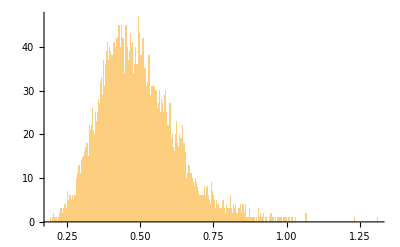

```mathematica
tTh =(# κ/(1+κ)/.κ-> κSpice)&/@RandomVariate[LogNormalDistribution[0,√(2 σn^2)]/.σn->σnSpice,10^4];
Histogram[tTh, 1000]
```

τ distribution

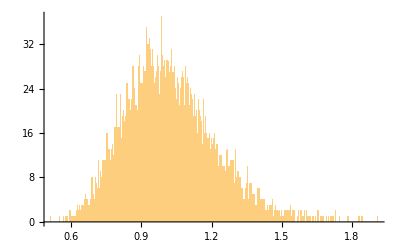

```mathematica
tTau =(#^κ τ/.{κ-> κSpice, τ-> 1})&/@RandomVariate[LogNormalDistribution[0,σn/κ]/.{κ-> κSpice, σn->σnSpice},10^4];
Histogram[tTau, 1000]
```

F-I curves (no synapse)

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v_soma near {v_soma} = {0.105851}. NIntegrate obtained -207.253 and 207.552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v_soma near {v_soma} = {2.65735}. NIntegrate obtained -7.50842 and 10.2601 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v_soma near {v_soma} = {0.354526}. NIntegrate obtained 29.5647 and 36.9252 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

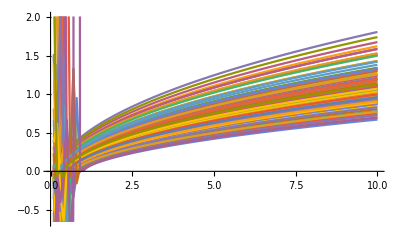

```mathematica
tFI=Table[freqSoma[Subscript[i, in],1, κSpice, #[[1]],  #[[2]],#[[3]]],{Subscript[i, in],0.1,10,0.1}]&/@Transpose[{RandomVariate[LogNormalDistribution[0,σn/κ]/.{κ-> κSpice, σn-> σnSpice},100], RandomVariate[LogNormalDistribution[0,√(σn^2+2 σp^2)]/.{σn-> σnSpice, σp-> σpSpice},100], RandomVariate[LogNormalDistribution[0,√(2 σn^2)]/.σn->σnSpice,100]}];
ListLinePlot[tFI, DataRange->{0.1, 10}]
```

## Scratchpad

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v_soma near {v_soma} = {1.00006}. NIntegrate obtained 96177.5 and 80502.5 for the integral and error estimates.

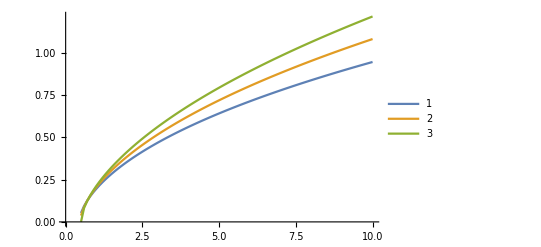

```mathematica
tFI=Table[Table[freqSoma[Subscript[i, in], 1, κ, 1, 1, 1], {Subscript[i, in], 0.5, 10, 0.1}], {κ, 0.8, 1.0, 0.1}];
ListLinePlot[tFI, DataRange->{0.5, 10}, PlotLegends->Automatic]
```

The distribution of I_soma^2/I_leaksoma

```mathematica
TransformedDistribution[ (rv1 rv2)/rv3, rv1\[Distributed]iDistStages[Subscript[I, soma],0, σnB, σpB, 1, 0]&&rv2\[Distributed]iDistStages[Subscript[I, soma],0, σn, σp, 1, 2]&&rv3\[Distributed]iDistStages[Subscript[I, leaksoma],0, σn, σp, 1, 0]]/.σnB-> 0
```

LogNormalDistribution[-Log[I_leaksoma]+2 Log[I_soma],√(2 σn^2+2 σp^2)]

```mathematica
Subscript[I, mem]^(1/κ-1)Subscript[I, mem]^2/Subscript[I, leaksoma]/(((1+κ) Subscript[Λ, fb])/Subscript[I, leaksoma])^(-1/κ)1/(1+κ)
```

(I_mem^(1+1/κ) (((1+κ) Λ_fb)/I_leaksoma)^(1/κ))/(I_leaksoma (1+κ))

```mathematica
Subscript[I, mem]^(1/κ)Subscript[I, mem]/Subscript[I, leaksoma]/(((1+κ) Subscript[Λ, fb])/Subscript[I, leaksoma])^(-1/κ)1/(1+κ)
```

(I_mem^(1+1/κ) (((1+κ) Λ_fb)/I_leaksoma)^(1/κ))/(I_leaksoma (1+κ))

```mathematica
FullSimplify[{vMem[Subscript[J, mem], Subscript[I, leaksoma], Subscript[Λ, fb]], vMem[Subscript[J, mem], Subscript[I, leaksoma], Subscript[Λ, fb]]^κ}/.Subscript[J, mem]-> Subscript[I, mem]^(1/κ), Subscript[I, leaksoma]>0&&κ>0]
```

{((I_mem (1+κ) Λ_fb)/I_leaksoma)^(1/κ),(I_mem (1+κ) Λ_fb)/I_leaksoma}

```mathematica
FullSimplify[TransformedDistribution[#,rv1\[Distributed]iDistStages[Subscript[I, soma],0, σn1, σp1, 1, 2]&&rv2\[Distributed]iDistStages[Subscript[I, leaksoma],0, σn2, σp2, 1, 0]]]&/@ {rv1^(1/κ)/rv2^(1/κ), rv1/rv2}
```

{LogNormalDistribution[(-Log[I_leaksoma]+Log[I_soma])/κ,(√(σn1^2+σn2^2+2 σp1^2))/κ],LogNormalDistribution[-Log[I_leaksoma]+Log[I_soma],√(σn1^2+σn2^2+2 σp1^2)]}

```mathematica
TransformedDistribution[rv2/rv1,rv1\[Distributed]iDistStages[Subscript[I, bg],0, σn1, σp1, 1, 0]&&rv2\[Distributed]iDistStages[Subscript[I, leaksoma],0, σn2, σp2, 1, 0]]
```

LogNormalDistribution[-Log[I_bg]+Log[I_leaksoma],√(σn1^2+σn2^2)]

```mathematica
TransformedDistribution[a rv1, rv1 \[Distributed]LogNormalDistribution[μ, σ]]
```

LogNormalDistribution[μ+Log[a],σ]

Notes

v_soma is in reality α v_soma, where α is deterministally determined by the random variable i_leaksoma (α==(I_leaksoma/i_leaksoma)^(1/κ)) and will have a distribution LogNormalDistribution[0, σn/κ]. v_soma^κ is in reality (β(α v_soma))^κ, where β is a random variable drawn from LogNormalDistribution[0,√(σn^2+2 σp^2)] (independent of I_leaksoma, since, for a given I_leaksoma, v_mem^κ is only influenced by mismatch in I_soma). Similarly τ is in reality α^κ τ.

```mathematica
tFI=Table[freqSoma[Subscript[i, in],0.899,1, #[[1]], #[[2]]],{Subscript[i, in],0.5,10,0.1}]&/@Transpose[{RandomVariate[LogNormalDistribution[0,σn/κ]/.{κ-> 0.9, σn-> 0.1},100], RandomVariate[LogNormalDistribution[0,√(σn^2+2 σp^2)]/.{κ-> 0.9, σn-> 0.1, σp-> 0.1},100]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.903402}. NIntegrate obtained 93.4974 and 177.886 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.684255}. NIntegrate obtained 1.65579 and 18.6949 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.984557}. NIntegrate obtained -29.8316 and 54.1247 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.054093,0.113904,0.157348,0.194321,0.227392,0.257722,0.285964,0.312536,80,1.35154,1.36009,1.3686,1.37706,1.38547,1.39384,1.40217,1.41046},98,{1}}
 |  |  |  |

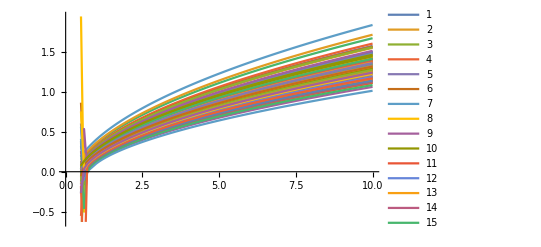

```mathematica
ListLinePlot[tFI, DataRange->{0.5, 10}, PlotLegends->Automatic]
```